```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=2;
PI=N[π,12];
θ=7PI/16;
α=3PI/5;
β=7PI/11;
(*α=3PI/16;
β=PI/8;*)
Ns=200;
```

## QC

```mathematica
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Memristor Circuit

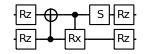

```mathematica
circMR={Subscript[Rz, 0][θ],Subscript[Rz, 1][θ],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 1][Subscript[Rx, 0][PI-2θ]],Subscript[S, 1],Subscript[Rz, 1][-θ],Subscript[Rz, 0][-θ]};
DrawCircuit@circMR
```

## Exchange Circuit

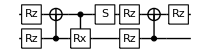

```mathematica
circEX=Join[circMR,{Subscript[C, 0][Subscript[X, 1]],Subscript[Rz, 1][-θ]}];
DrawCircuit@circEX
```

## Initialisation Map

```mathematica
P0={{1,0},{0,0}};
SP={{0,1},{0,0}};
INI={P0,SP};
```

## Encoding

```mathematica
InitZeroState[ρIN];
circ={Subscript[Kraus, 1][INI],Subscript[Rx, 1][α],Subscript[Rz, 1][β]};
ApplyCircuit[circ,ρIN,ρOUT];
XC=CalcExpecPauliSum[ρOUT,Subscript[X, 1],ρWP];
YC=CalcExpecPauliSum[ρOUT,Subscript[Y, 1],ρWP];
ZC=CalcExpecPauliSum[ρOUT,Subscript[Z, 1],ρWP];
```

```mathematica
EncodingX={1};
EncodingY={0};
EncodingZ={0};
InitZeroState[ρIN];
circ={Subscript[H, 0]};
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
Do[(
circ={Subscript[Kraus, 1][INI],Subscript[Rx, 1][α],Subscript[Rz, 1][β]};
circ=Join[circ,circEX];
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
XM=CalcExpecPauliSum[ρOUT,Subscript[X, 0],ρWP];
YM=CalcExpecPauliSum[ρOUT,Subscript[Y, 0],ρWP];
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[EncodingX,XM];
AppendTo[EncodingY,YM];
AppendTo[EncodingZ,ZM];
),{i,Ns}];
```

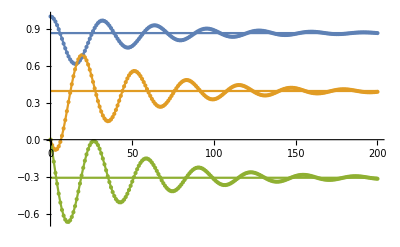

```mathematica
plotS=ListPlot[{Transpose[{Range[0,Ns],EncodingX}],Transpose[{Range[0,Ns],EncodingY}],Transpose[{Range[0,Ns],EncodingZ}]}];
plotL=ListLinePlot[{Transpose[{Range[0,Ns],EncodingX}],Transpose[{Range[0,Ns],EncodingY}],Transpose[{Range[0,Ns],EncodingZ}]}];
plotIN=ListLinePlot[{{{0,XC},{Ns,XC}},{{0,YC},{Ns,YC}},{{0,ZC},{Ns,ZC}}}];
Show[plotS,plotL,plotIN,PlotRange->All]
```

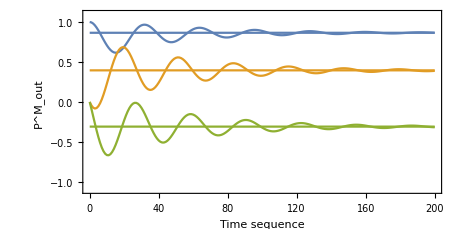

```mathematica
plotL=ListLinePlot[{Transpose[{Range[0,Ns],EncodingX}],Transpose[{Range[0,Ns],EncodingY}],Transpose[{Range[0,Ns],EncodingZ}]},PlotRange->{{0,200},{-1.1,1.1}},Axes->{False,False},Frame->True,FrameLabel->{"Time sequence","P^M_out"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18},AspectRatio->1/2];
plotIN=ListLinePlot[{{{0,XC},{Ns,XC}},{{0,YC},{Ns,YC}},{{0,ZC},{Ns,ZC}}}];
Show[plotL,plotIN]
```